0.380506

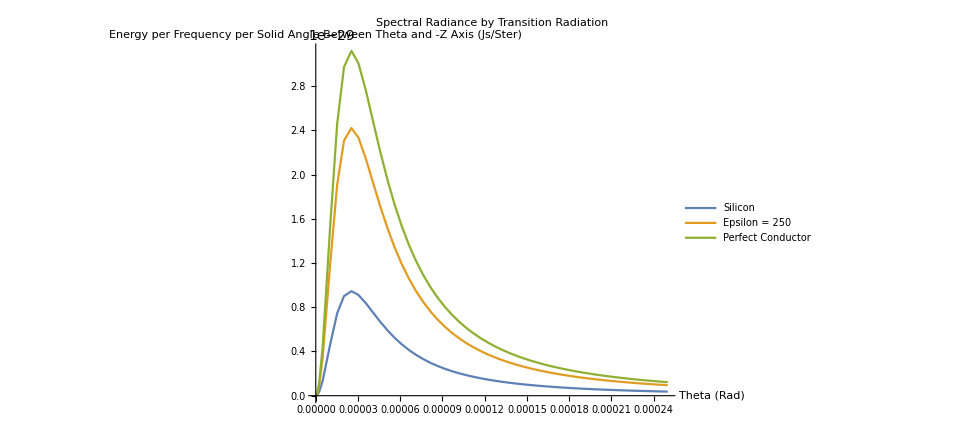

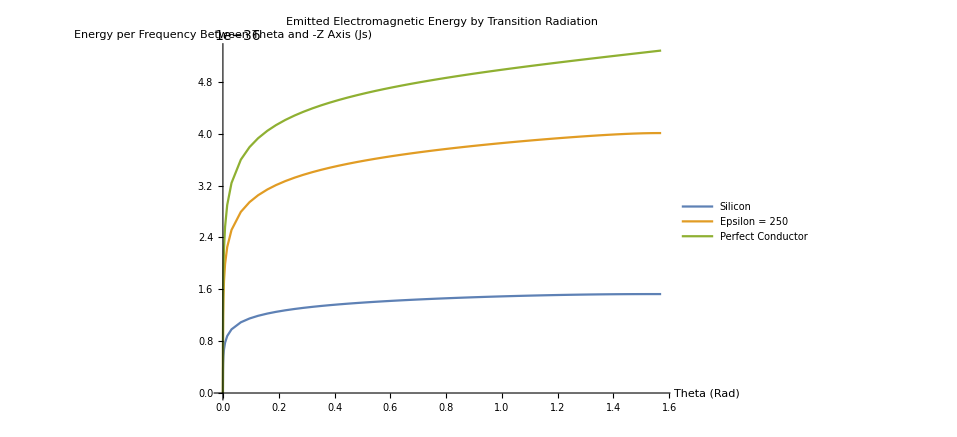

0.0214108

0.0241286

9.58604×10^-21

0.887362

0.0549094

0.0633973

2.51871×10^-20

0.866115

0.0707742

0.0835257

3.31839×10^-20

0.847334

7.29978×10^-18

$Aborted

$Aborted

$Aborted

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
a=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
rad=0.02; (*radius of diffraction radiation hole in m*)
lowerlambda=300;(*Visible Spectrum nm*)
averagelambda=500;
upperlambda=700;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;

thetalens=ArcTan[a/d]
thetamax=1/gamma;

lowerfreq=2*Pi*c/(upperlambda*1*^9);
averagefreq=2*Pi*c/(averagelambda*1*^-9);
upperfreq=2*Pi*c/(lowerlambda*1*^-9);
Fn[theta_,eps1_,eps2_,beta_]:=
(eps2-eps1)*(1-beta^2*eps1+beta*Sqrt[eps2-eps1*Sin[theta]^2])
Fd[theta_,eps1_,eps2_,beta_]:=
(1-beta^2eps1*Cos[theta]^2)*(1+beta*Sqrt[eps2-eps1*Sin[theta]^2])*(eps2*Cos[theta]+Sqrt[eps1*eps2-eps1^2*Sin[theta]^2])
dWdwdomega[theta_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
1/(4 *Pi*eps0)*e^2*beta^2/(Pi^2*c)*Sqrt[eps1]*Sin[theta]^2*Cos[theta]^2*((eps2-eps1)*(1-beta^2*eps1+beta*Sqrt[eps2-eps1*Sin[theta]^2]))^2/((1-beta^2eps1*Cos[theta]^2)*(1+beta*Sqrt[eps2-eps1*Sin[theta]^2])*(eps2*Cos[theta]+Sqrt[eps1*eps2-eps1^2*Sin[theta]^2]))^2
dWdw[theta_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
1/(4 *Pi*eps0)*(2*Pi*Sin[theta])*e^2*beta^2/(Pi^2*c)*Sqrt[eps1]*Sin[theta]^2*Cos[theta]^2*((eps2-eps1)*(1-beta^2*eps1+beta*Sqrt[eps2-eps1*Sin[theta]^2]))^2/((1-beta^2eps1*Cos[theta]^2)*(1+beta*Sqrt[eps2-eps1*Sin[theta]^2])*(eps2*Cos[theta]+Sqrt[eps1*eps2-eps1^2*Sin[theta]^2]))^2
dWdwdomegaideal[theta_,gamma_,e_,c_,beta_]:=
1/(4 *Pi*eps0)*e^2*beta^2*Sin[theta]^2/(Pi^2*c*(1-beta^2*Cos[theta]^2)^2)
dWdwideal[theta_,gamma_,e_,c_,beta_]:=
1/(4 *Pi*eps0)e^2/(2*Pi*c)*((2*(1-beta^2)*Cos[theta]/(1-beta^2*Cos[theta]^2))+((1+beta^2)/beta)*Log[((1-beta*Cos[theta])*(1+beta)/((1+beta*Cos[theta])*(1-beta)))]-2)


dWdwdiff[theta_,r_,rad_,w_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
dWdwdomega[theta,gamma,eps1,eps2,e,c,beta]*(BesselJ[0,w/c*rad*Sin[theta]]^2+(r/rad)^2*BesselJ[1,w/c*rad*Sin[theta]])
dWdwdiffideal[theta_,r_,rad_,w_,gamma_,e_,c_,beta_]:=
dWdwdomegaideal[theta,gamma,e,c,beta]*(BesselJ[0,w/c*rad*Sin[theta]]^2+(r/rad)^2*BesselJ[1,w/c*rad*Sin[theta]])
dWdomegadiff[theta_,r_,rad_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
NIntegrate[dWdwdiff[theta,r,rad,w,gamma,eps1,eps2,e,c,beta],{w,lowerfreq,upperfreq}]
dWdomegadiffideal[theta_,r_,rad_,gamma_,e_,c_,beta_]:=
NIntegrate[dWdwdiffideal[theta,r,rad,w,gamma,e,c,beta],{w,lowerfreq,upperfreq}]
Energydiff[r_,rad_,thetaa_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
NIntegrate[(2*Pi*Sin[theta])*dWdwdiff[theta,r,rad,w,gamma,eps1,eps2,e,c,beta],{theta,0,thetaa},{w,lowerfreq,upperfreq}]
Energydiffideal[r_,rad_,thetaa_,gamma_,e_,c_,beta_]:=
NIntegrate[(2*Pi*Sin[theta])*dWdwdiffideal[theta,rad,r,w,gamma,e,c,beta],{theta,0,thetaa},{w,lowerfreq,upperfreq}]
Dens[r_,z_,sigx_,sigy_,sigz_]:=
1/(sigx*sigy*sigz)*Exp[-1/2*(r^2/sigx^2+z^2/sigz^2)]
Energytotaldiff[r_,z_,rad_,sigx_,sigy_,sigz_,thetaa_,gamma_,eps1_,eps2_,e_,c_,beta_]:=
2*Pi*Dens[r,z,sigx,sigy,sigz]*Energydiff[r,rad,thetaa,gamma,eps1,eps2,e,c,beta]
Energytotaldiffideal[r_,z_,rad_,sigx_,sigy_,sigz_,thetaa_,gamma_,e_,c_,beta_]:=
2*Pi*Dens[r,z,,sigx,sigy,sigz]*Energydiffideal[r,rad,thetaa,gamma,e,c,beta]




plot1=Plot[{dWdwdomega[theta,gamma,eps1,eps2,e,c,beta],dWdwdomega[theta,gamma,eps1,eps3,e,c,beta],dWdwdomegaideal[theta,gamma,e,c,beta]},{theta,0,10/gamma},AxesLabel-> {"Theta (Rad)","Energy per Frequency per Solid Angle Between Theta and -Z Axis (Js/Ster)"},PlotLabel->Style["Spectral Radiance by Transition Radiation",FontSize->18],PlotLegends->Placed[{"Silicon","Epsilon = 250","Perfect Conductor"},{Center,Right}]]
plot2=Plot[{NIntegrate[dWdw[theta0,gamma,eps1,eps2,e,c,beta],{theta0,0,theta}],NIntegrate[dWdw[theta0,gamma,eps1,eps3,e,c,beta],{theta0,0,theta}],dWdwideal[theta,gamma,e,c,beta]},{theta,0,Pi/2},AxesLabel-> {"Theta (Rad)","Energy per Frequency Between Theta and -Z Axis (Js)"},PlotLabel->Style["Emitted Electromagnetic Energy by Transition Radiation",FontSize->18],PlotLegends->Placed[{"Silicon","Epsilon = 250","Perfect Conductor"},{Center,Right}]]

energy=NIntegrate[dWdw[theta,gamma,eps1,eps2,e,c,beta],{theta,0,thetalens}];
energytotal=NIntegrate[dWdw[theta,gamma,eps1,eps2,e,c,beta],{theta,0,Pi/2}];
energyti=NIntegrate[dWdw[theta,gamma,eps1,eps3,e,c,beta],{theta,0,thetalens}];
energytotalti=NIntegrate[dWdw[theta,gamma,eps1,eps3,e,c,beta],{theta,0,Pi/2}];

photon=(upperfreq-lowerfreq)*energy/(hbar*averagefreq)
photontotal=(upperfreq-lowerfreq)*energytotal/(hbar*averagefreq)
energyvisible=(upperfreq-lowerfreq)*energytotal
ratio=photon/photontotal

photonti=(upperfreq-lowerfreq)*energyti/(hbar*averagefreq)
photontotalti=(upperfreq-lowerfreq)*energytotalti/(hbar*averagefreq)
energyvisibleti=(upperfreq-lowerfreq)*energytotalti
ratioti=photonti/photontotalti

photonideal=(upperfreq-lowerfreq)*dWdwideal[thetalens,gamma,e,c,beta]/(hbar*averagefreq)
photonidealtotal=(upperfreq-lowerfreq)*dWdwideal[Pi/2,gamma,e,c,beta]/(hbar*averagefreq)
energyvisibleideal=(upperfreq-lowerfreq)*dWdwideal[Pi/2,gamma,e,c,beta]
ratioideal=photonideal/photonidealtotal



dWdomegadiffideal[rad/2,Pi/2,rad,gamma,e,c,beta]
Energydiffideal[rad/2,rad,thetalens,gamma,e,c,beta]
NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,thetalens,gamma,eps1,eps2,e,c,beta],{r,0,1},{z,-Infinity,Infinity}]

plot3=Plot[{dWdomegadiff[theta,0,rad,gamma,eps1,eps2,e,c,beta],dWdomegadiff[theta,0,rad,gamma,eps1,eps3,e,c,beta],dWdomegadiffideal[theta,0,rad,gamma,e,c,beta]},{theta,0,10/gamma},AxesLabel-> {"Theta (Rad)","Energy per Solid Angle Between Theta and -Z Axis (J/Ster)"},PlotLabel->"Emitted Optical Electromagnetic Energy by Diffraction Radiation at r = 0",PlotLegends->{"Silicon","Epsilon = 250","Perfect Conductor"}]
(*plot4=Plot[{Energydiff[r,rad,Pi/2,gamma,eps1,eps2,e,c,beta],Energydiff[r,rad,Pi/2,gamma,eps1,eps3,e,c,beta],Energydiffideal[r,rad,Pi/2,gamma,e,c,beta]},{r,0,rad},AxesLabel-> {"Radius (m)","Total Optical Energy Emitted at Radius R (J)"},PlotLabel->"Emitted Optical Electromagnetic Energy by Diffraction Radiation at Radius R",PlotLegends->{"Silicon","Titanium","Perfect Conductor"}]
plot5=Plot[{NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,theta,gamma,eps1,eps2,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}],NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,theta,gamma,eps1,eps3,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}],NIntegrate[Energytotaldiffideal[r,z,rad,sigx,sigy,sigz,theta,gamma,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}]},{theta,0,Pi/2},AxesLabel-> {"Theta (Rad)","Total Optical Energy Collected (J)"},PlotLabel->"Collected Optical Electromagnetic Energy by Diffraction Radiation Between Theta and -Z Axis",PlotLegends->{"Silicon","Titanium","Perfect Conductor"}]


energydiff=NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,thetalens,gamma,eps1,eps2,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];
energytotaldiff=NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,Pi/2,gamma,eps1,eps2,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];
energydiffti=NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,thetalens,gamma,eps1,eps3,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];
energytotaldiffti=NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,Pi/2,gamma,eps1,eps3,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];
energyidealdiff=NIntegrate[Energytotaldiffideal[r,z,rad,sigx,sigy,sigz,thetalens,gamma,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];
energytotalidealdiff=NIntegrate[Energytotaldiffideal[r,z,rad,sigx,sigy,sigz,Pi/2,gamma,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}];

photondiff=energydiff/(hbar*averagefreq)
photontotaldiff=energytotaldiff/(hbar*averagefreq)
energyvisiblediff=energytotaldiff
ratiodiff=photondiff/photontotaldiff

photondiffti=energydiffti/(hbar*averagefreq)
photontotaldiffti=energytotaldiffti/(hbar*averagefreq)
energyvisiblediffti=energytotaldiffti
ratiodiffti=photondiffti/photontotaldiffti

photonidealdiff=energyidealdiff/(hbar*averagefreq)
photonidealtotaldiff=energytotalidealdiff/(hbar*averagefreq)
energyvisibleidealdiff=energytotalidealdiff
ratioidealdiff=photonidealdiff/photonidealtotaldiff

plot5=Plot[{NIntegrate[dWdw[theta0,gamma,eps1,eps2,e,c,beta],{theta0,0,theta}],NIntegrate[dWdw[theta0,gamma,eps1,eps3,e,c,beta],{theta0,0,theta}],dWdwideal[theta,gamma,e,c,beta],NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,theta,gamma,eps1,eps2,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}],NIntegrate[Energytotaldiff[r,z,rad,sigx,sigy,sigz,theta,gamma,eps1,eps3,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}],NIntegrate[Energytotaldiffideal[r,z,rad,sigx,sigy,sigz,theta,gamma,e,c,beta],{r,0,Infinity},{z,-Infinity,Infinity}]},{theta,0,Pi/2},AxesLabel-> {"Theta (Rad)","Total Optical Energy Collected (J)"},PlotLabel->"Collected Optical Electromagnetic Energy by Radiation Between Theta and -Z Axis",PlotLegends->{"Transition Silicon","Tranisition Titanium","Transition Perfect Conductor","Diffraction Silicon","Diffraction Titanium","Diffraction Perfect Conductor"}]*)


(*varinputnames={"Gamma","Beta","Dielectric Constant","Number of Electrons","Bunch Charge (Coulombs)","Lens Diameter (m)","Distance to Lens (m)"};
varinput={gamma,beta,eps2,n,q,a,d};
varoutputnames={"Angle Coverage of Lens (Rad)","Maximum Angle (Rad)""Number of Photons (Dielectric)","Number of Photons Total (Dielectric)","Total Visible Energy (Dielectric)","Number of Photons (Ideal)","Number of Photons Total (Ideal)","Total Visible Energy (Ideal)","Ratio (Dielectric)","Ratio (Ideal)"};
varoutput={thetalens,thetamax,photon,photontotal,energyvisible,photonideal,photonidealtotal,energyvisibleideal,ratio,ratioideal};

export1=Export["dWdwdomega.jpg",plot1]
export2=Export["dWdw.jpg",plot2]
Save["dWdwdomega.jpg",export1]
Save["dWdw.jpg",export2]

OpenWrite["photondata"]
Write["photondata",varinputnames]
Export["photondata",varinputnames]

OpenWrite["photondata.txt"];
Export["photondata.txt",{varinputnames}]
OpenRead["photondata.txt"]*)
```

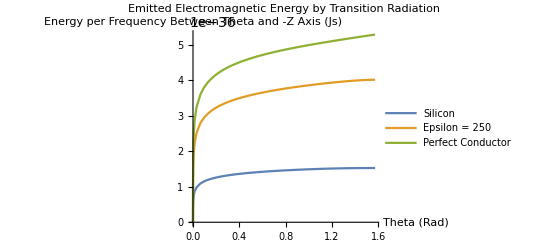
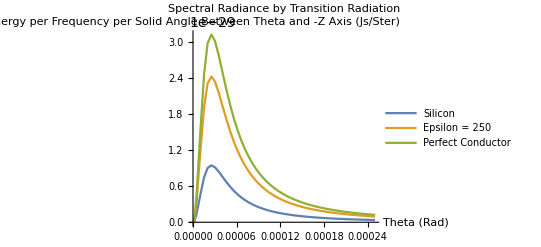

0.0214108

0.0241286

9.58604×10^-21

0.887362

0.0549094

0.0633973

2.51871×10^-20

0.866115

0.0707742

0.0835257

3.31839×10^-20

0.847334

7.29978×10^-18

$Aborted

$Aborted

$Aborted

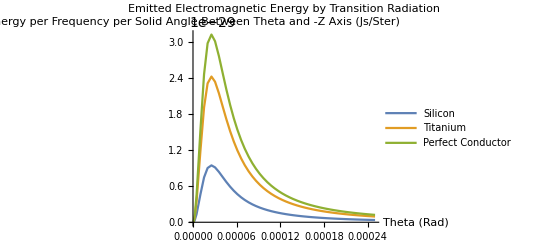

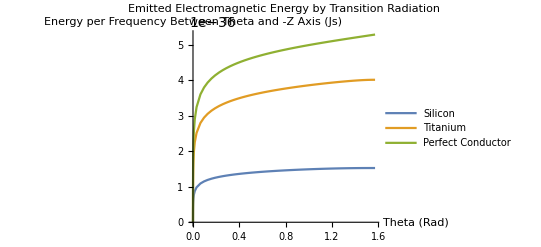

0.0214108

0.0241286

9.58604×10^-21

0.887362

0.0549094

0.0633973

2.51871×10^-20

0.866115

0.0707742

0.0835257

3.31839×10^-20

0.847334

7.29978×10^-18

$Aborted

$Aborted

$Aborted

```mathematica
SystemOpen[export2]
```

```mathematica
SystemOpen["dWdw.jpg"]
```

```mathematica
NIntegrate[dWdwdomegaideal[theta,40000,1.602*^-19,3*^8,Sqrt[1-1/40000^2]]*2*Pi*Sin[theta],{theta,0,Pi/2}]
```

```mathematica
5.876199836523489*^-46
dWdwideal[Pi/s,40000,1.602*^-19,3*^8,Sqrt[1-1/40000^2]
```

5.8762×10^-46

```mathematica
dWdw[Pi/8,40000,1,11.9,1.602*^-19,3*^8,Sqrt[1-1/40000^2]]
Clear[dWdw]
```

1.89921×10^-46

```mathematica
dWdw[Pi/8,40000,1,11.9,1.602*^-19,3*^8,Sqrt[1-1/40000^2]]//N
```

dWdw[0.392699,40000.,1.,11.9,1.602×10^-19,3.×10^8,1.]

```mathematica
dW_dw[Pi/8,40000,1,11.9,1.602*^-19,3*^8,Sqrt[1-1/40000^2]]
```

dW_dw[π/8,40000,1,11.9,1.602×10^-19,300000000,(√1599999999)/40000]

```mathematica
dW_dw[Pi/8,40000,1,11.9,1.602*^-19,3*^8,Sqrt[1-1/40000^2]]//N
```

dW_dw[0.392699,40000.,1.,11.9,1.602×10^-19,3.×10^8,1.]

```mathematica
dW_dw[Pi/8,40000,1,11.9]
```

dW_dw[π/8,40000,1,11.9]

```mathematica
f[x,x^2]
```

f[x,x^2]

```mathematica
f[2]
```

f[2]

```mathematica
f[x,x^2]=:y
```

```mathematica
f[x,x^2]:=y
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f[x]:=x^3
```

```mathematica
f[3]
```

9

```mathematica
f
```

```mathematica
f[2]
```

f[2]

```mathematica
y
```

y

```mathematica
dW_dw[Pi/8,40000,1,11.9]
```

dW_dw[π/8,40000,1,11.9]

```mathematica
dW_dw[Pi/8,40000,1,11.9]
```

dW_dw[π/8,40000,1,11.9]

```mathematica
dW_dw[Pi/8,40000,1,11.9]
```

dW_dw[π/8,40000,1,11.9]